```mathematica
sVars={"i","j","k","l"};tVars={"m","n"};

Phi[x_]=1/2 (1+Erf[x/(√2)]);
(*Averages in case of an Erf teacher and student needed in order to formulate the dynamics and compute the generalization error*)
I2Erf[C2_]:=(2 ArcSin[C2⟦1,2⟧/(√(1+C2⟦1,1⟧) √(1+C2⟦2,2⟧))])/π;
I3Erf[C3_]:=(2 (C3⟦2,3⟧ (1+C3⟦1,1⟧)-C3⟦1,2⟧ C3⟦1,3⟧))/(π √((1+C3⟦1,1⟧) (1+C3⟦3,3⟧)-C3⟦1,3⟧^2) (1+C3⟦1,1⟧));
I4Erf[C4_]:=Module[{Λ0,Λ1,Λ2,Λ4},Λ4=(1+C4⟦1,1⟧) (1+C4⟦2,2⟧)-C4⟦1,2⟧^2;Λ0=Λ4 C4⟦3,4⟧-C4⟦2,3⟧ C4⟦2,4⟧ (1+C4⟦1,1⟧)-C4⟦1,3⟧ C4⟦1,4⟧ (1+C4⟦2,2⟧)+C4⟦1,2⟧ C4⟦1,3⟧ C4⟦2,4⟧+C4⟦1,2⟧ C4⟦1,4⟧ C4⟦2,3⟧;Λ1=Λ4 (1+C4⟦3,3⟧)-C4⟦2,3⟧^2 (1+C4⟦1,1⟧)-C4⟦1,3⟧^2 (1+C4⟦2,2⟧)+2 C4⟦1,2⟧ C4⟦1,3⟧ C4⟦2,3⟧;Λ2=Λ4 (1+C4⟦4,4⟧)-C4⟦2,4⟧^2 (1+C4⟦1,1⟧)-C4⟦1,4⟧^2 (1+C4⟦2,2⟧)+2 C4⟦1,2⟧ C4⟦1,4⟧ C4⟦2,4⟧;Return[(4 ArcSin[Λ0/(√Λ1 √Λ2)])/(π^2 √Λ4)];];
(*Averages in case of a ReLU teacher and student*)
I2ReLU[C2_]:=1/4 C2⟦1,2⟧+(√(C2⟦1,1⟧ C2⟦2,2⟧-C2⟦1,2⟧^2))/(2 π)+(C2⟦1,2⟧ ArcSin[C2⟦1,2⟧/(√(C2⟦1,1⟧ C2⟦2,2⟧))])/(2 π);
I3ReLU[C3_]:=(C3⟦1,2⟧ √(C3⟦1,1⟧ C3⟦3,3⟧-C3⟦1,3⟧^2))/(2 π C3⟦1,1⟧)+(C3⟦2,3⟧ ArcSin[C3⟦1,3⟧/(√(C3⟦1,1⟧ C3⟦3,3⟧))])/(2 π)+1/4 C3⟦2,3⟧;
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];

(*NOT IMPORTANT FOR NOW: Ignore the following averages, experimental*)
I4ReLU11[C2_]:=1/4 C2⟦2⟧⟦2⟧+(((C2⟦1⟧⟦2⟧)/(C2⟦1⟧⟦1⟧)-2) √(C2⟦1⟧⟦1⟧ C2⟦2⟧⟦2⟧-(C2⟦1⟧⟦2⟧)^2))/(2 π)+((C2⟦2⟧⟦2⟧-2 C2⟦1⟧⟦2⟧) ArcSin[(C2⟦1⟧⟦2⟧)/(√(C2⟦2⟧⟦2⟧ C2⟦1⟧⟦1⟧))])/(2 π)-1/2 C2⟦1⟧⟦2⟧+1/2 C2⟦1⟧⟦1⟧;
I2ErfReLU[C2_]:=C2⟦1,2⟧/(√(2 π) √(1+C2⟦2,2⟧));
I3ErfReLU[C3_]:=C3⟦2,3⟧/(√(2 π) √(1+C3⟦2,2⟧));
I3ReLUErf[C3_]:=(√(2/π) (-C3⟦1,2⟧ C3⟦1,3⟧+(1+C3⟦1,1⟧) C3⟦2,3⟧))/(√(2 π) (1+C3⟦1,1⟧)^(3/2));
HelperReLU[varList_]:=Return[0];

(*Not important: This section deals with returning the correct symbol (order parameter) for a covariance between two variables*)
getCovar[var1_,var2_]:=(If[MemberQ[sVars,First[var1]],If[MemberQ[sVars,First[var2]],If[Last[var1]≤Last[var2],Return[Subscript[Q, Last[var1],Last[var2]][α]],Return[Subscript[Q, Last[var2],Last[var1]][α]]],Return[Subscript[R, Last[var1],Last[var2]][α]]],If[MemberQ[sVars,First[var2]],Return[Subscript[R, Last[var2],Last[var1]][α]],Return[T⟦Last[var1],Last[var2]⟧]]];);

createCoVar[varList_]:=Module[{returnMat,r,c},d=Length[varList];returnMat=ConstantArray[0,{d,d}];For[r=1,r≤d,r++,For[c=r,c≤d,c++,returnMat⟦r,c⟧=If[d==2,getCovar[varList⟦r⟧,varList⟦c⟧],getCovar[varList⟦r⟧,varList⟦c⟧]];returnMat⟦c,r⟧=returnMat⟦r,c⟧;]];returnMat];

(*IMPORTANT: This function formulates the dynamical equations for the desired system*)

FormulateDynamics[actTeach_,actStud_,δ_,γ_]:=Module[{eqnsR,eqnsQ,eqnsv,eg},
(*Dit bepaalt welke activatiefuncties er gebruikt worden in de averages, voor als student en teacher verschillende activatiefuncties hebben
TODO: Simplify significantly*)
Switch[actStud,
"ReLU",I2Stud=I2ReLU;I3Stud=I3ReLU;I4=HelperReLU;assumps=Flatten[{RAssumptionsReLU,QAssumptionsReLU}];If[actTeach=="ReLU",I2Teach=I2ReLU;I2Cross=I2ReLU;I3Teach=I3ReLU;I4Teach=I4ReLU;,I2Teach=I2Erf;I2Cross=I2ErfReLU;I3Teach=I3ErfReLU;],
"Erf",I2Stud=I2Erf;I3Stud=I3Erf;I4Stud=I4Erf;If[actTeach=="ReLU",I2Teach=I2ReLU;I2Cross=I2ErfReLU;I3Teach=I3ReLUErf;assumps=Flatten[{RAssumptionsReLU,QAssumptionsReLU}],I2Teach=I2Erf;I2Cross=I2Erf;I3Teach=I3Erf;I4Teach=I4Erf]];
(*ODE first layer*)
(*Here the equations are formulated using the correct averages I2, I3 and I4*)
eqnsR=Flatten[Table[Subscript[R, i,n]'[α]==Simplify[η (∑_m^M I3Teach[createCoVar[{{"i",i},{"n",n},{"m",m}}]]-∑_j^K I3Stud[createCoVar[{{"i",i},{"n",n},{"j",j}}]])-(δ+γ)Subscript[R, i,n][α],assumps],{i,1,K},{n,1,M}]];eqnsQ =Flatten[Table[Subscript[Q, i,k]'[α]==Simplify[η (∑_m^M I3Teach[createCoVar[{{"i",i},{"k",k},{"m",m}}]]-∑_j^K I3Stud[createCoVar[{{"i",i},{"k",k},{"j",j}}]]+∑_m^M I3Teach[createCoVar[{{"k",k},{"i",i},{"m",m}}]]-∑_j^K I3Stud[createCoVar[{{"k",k},{"i",i},{"j",j}}]])+η^2 (∑_m^M ∑_n^M I4Teach[createCoVar[{{"i",i},{"k",k},{"n",n},{"m",m}}]]-2 ∑_n^M ∑_j^K I4Teach[createCoVar[{{"i",i},{"k",k},{"j",j},{"n",n}}]]+∑_l^K ∑_j^K I4Teach[createCoVar[{{"i",i},{"k",k},{"j",j},{"l",l}}]])-2γ Subscript[Q, i,k][α],assumps],{i,1,K},{k,i,K}]];
(*Onderstaand stuk is gebruikt voor de single-layer ReLU perceptron, omdat hiervoor de eta^2 term hoogstens 2d averages bevat.*)
(*η^2 I4ReLU11[{{Subscript[Q, 1,1][α],Subscript[R, 1,1][α]},{Subscript[R, 1,1][α],T⟦1⟧⟦1⟧}}]*) 
(*ODE second layer*)
eg[α_]:=1/2 (∑_(i=1)^K ∑_(j=1)^K I2Stud[createCoVar[{{"i",i},{"j",j}}]]-2 ∑_(i=1)^K ∑_(m=1)^M I2Cross[createCoVar[{{"i",i},{"m",m}}]]+∑_(m=1)^M ∑_(n=1)^M I2Teach[createCoVar[{{"m",m},{"n",n}}]]);
Return[<|R->eqnsR,Q->eqnsQ,generr->eg[α]|>]
];

createReLUAssumptions[M_,K_]:=(RAssumptionsReLU:=Table[(Subscript[R, i,m][α])^2≤Subscript[Q, i,i][α] T⟦m⟧⟦m⟧&&Subscript[R, i,m][α]∈Reals,{i,1,K},{m,1,M}];QAssumptionsReLU:=Table[Subscript[Q, i,j][α]^2≤Subscript[Q, i,i][α] Subscript[Q, j,j][α]&&Subscript[Q, i,j][α]∈Reals&&If[i==j,Subscript[Q, i,j][α]≥0],{i,1,K},{j,1,K}];);
```

-Graphics-

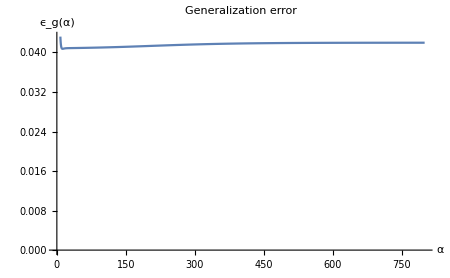

```mathematica
M=2;
(*Specifies properties of the teacher. Here, the weight vectors are orthonormal*)
T=IdentityMatrix[M];
K=2;
η=0.5;
(*Strength of drift and weight decay*)
δ=0.03;
γ=0;
(*The matrix of initial conditions for the differential equations (Macroscopic parameters*)
(*First layer macroscopics. Student-teacher overlaps and student-student overlaps respectively*)
R0=0.01;
X=10^-5;
Rinit = Table[Subscript[R, i,n][0]==R0+RandomVariate[UniformDistribution[{0,X}]],{i,1,K},{n,1,M}];
Qinit=Table[If[i==k,Subscript[Q, i,k][0]==0.5,Subscript[Q, i,k][0]==0.49],{i,1,K},{k,i,K}];
(*Symbols of functions that need to be solved for*)
Rs=Flatten[Table[Subscript[R, i,n],{i,K},{n,M}]];
Qs=Flatten[Table[Subscript[Q, i,k],{i,1,K},{k,i,K}]];
maxAlpha=800;
(*Formulates the dynamical equations*)
(*createReLUAssumptions[M,K];*)
ODEsys=FormulateDynamics["Erf","Erf",δ,γ];
(*Numerically solve the system ODEsystem*)
s=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];

(*Plot all Subscript[R, i,n], the inner products of student-teacher vectors*)
Rplot=Plot[Evaluate[Table[Subscript[R, i,n][α]/.s,{i,K},{n,M}]],{α,0,maxAlpha},PlotLegends->Placed[LineLegend[Rs],Below],PlotLabel->"Student-teacher overlap R",AxesOrigin->{0,0},AxesLabel->{α,"Overlap"},BaseStyle->{FontSize->14},ImageSize->450];
(*Plot the alignments of student-teacher vectors, so normalized by the lengths of vectors*)
Rhoplot=Plot[Evaluate[Table[Subscript[R, i,n][α]/Sqrt[Subscript[Q, i,i][α]*T[[n]][[n]]]/.s,{i,K},{n,M}]],{α,0,maxAlpha},PlotLegends->Placed[LineLegend[Rs],Below],PlotLabel->"Student-teacher alignments ρ",AxesOrigin->{0,0},AxesLabel->{α,"Overlap"},BaseStyle->{FontSize->14},ImageSize->450];

(*Plot all Subscript[Q, i,k] and the generalization errors*)
QPlot=Plot[Evaluate[Table[Subscript[Q, i,k][α]/.s,{i,1,K},{k,i,K}]],{α,0, maxAlpha},PlotLegends->Placed[LineLegend[Qs],Below],PlotLabel->"Student-student overlap Q",AxesOrigin->{0,0},AxesLabel->{α,"Overlap"},BaseStyle->{FontSize->14},ImageSize->450];
egPlot=Plot[Evaluate[ODEsys[generr]/.s],{α,0,maxAlpha},PlotLabel->"Generalization error",AxesOrigin->{0,0},AxesLabel->{α,Subscript[ϵ, g][α]},ImageSize->450,BaseStyle->{FontSize->14}];

GraphicsRow[{Rplot,Rhoplot},ImageSize->950]
GraphicsRow[{QPlot,egPlot},ImageSize->1150]
```

```mathematica
egerr[α_]=ODEsys[generr]/.s;
egerr[800]
```

0.746822

0.0419661

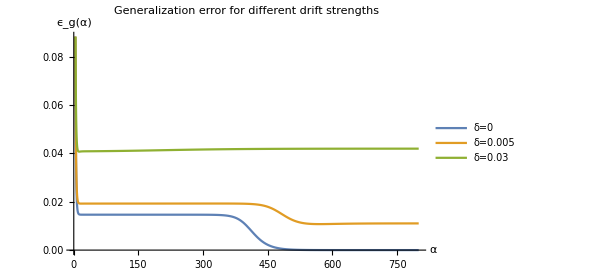

```mathematica
(*Get the last value of eg as an estimate for eg_infinity, assuming that we integrated for high enough maxAlpha*)
M=2;
(*Specifies properties of the teacher. Here, the weight vectors are orthonormal*)
T=IdentityMatrix[M];
K=2;
η=0.5;
(*Strength of drift and weight decay*)
δ=0;
γ=0;
(*The matrix of initial conditions for the differential equations (Macroscopic parameters*)
(*First layer macroscopics. Student-teacher overlaps and student-student overlaps respectively*)
R0=0.01;
X=10^-5;
Rinit = Table[Subscript[R, i,n][0]==R0+RandomVariate[UniformDistribution[{0,X}]],{i,1,K},{n,1,M}];
Qinit=Table[If[i==k,Subscript[Q, i,k][0]==0.5,Subscript[Q, i,k][0]==0.49],{i,1,K},{k,i,K}];
(*Symbols of functions that need to be solved for*)
Rs=Flatten[Table[Subscript[R, i,n],{i,K},{n,M}]];
Qs=Flatten[Table[Subscript[Q, i,k],{i,1,K},{k,i,K}]];
maxAlpha=800;
(*Formulates the dynamical equations*)
(*createReLUAssumptions[M,K];*)
ODEsys=FormulateDynamics["Erf","Erf",δ,γ];
(*Numerically solve the system ODEsystem*)
s1=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];

(*Slight real target drift*)
δ=0.005;
ODEsys=FormulateDynamics["Erf","Erf",δ,γ];
(*Numerically solve the system ODEsystem*)
s2=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];

(*Strong real target drift*)
δ=0.03;
ODEsys=FormulateDynamics["Erf","Erf",δ,γ];
(*Numerically solve the system ODEsystem*)
s3=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];

(*s1: solution no drift, s2: solution a bit of drift, s3: solution high drift*)
Plot[{Evaluate[ODEsys[generr]/.s1],Evaluate[ODEsys[generr]/.s2],Evaluate[ODEsys[generr]/.s3]},{α,0,maxAlpha},PlotLabel->"Generalization error for different drift strengths",AxesOrigin->{0,0},AxesLabel->{α,Subscript[ϵ, g][α]},ImageSize->450,BaseStyle->{FontSize->14},PlotLegends->Placed[LineLegend[{"δ=0","δ=0.005","δ=0.03"}],Below]]
```

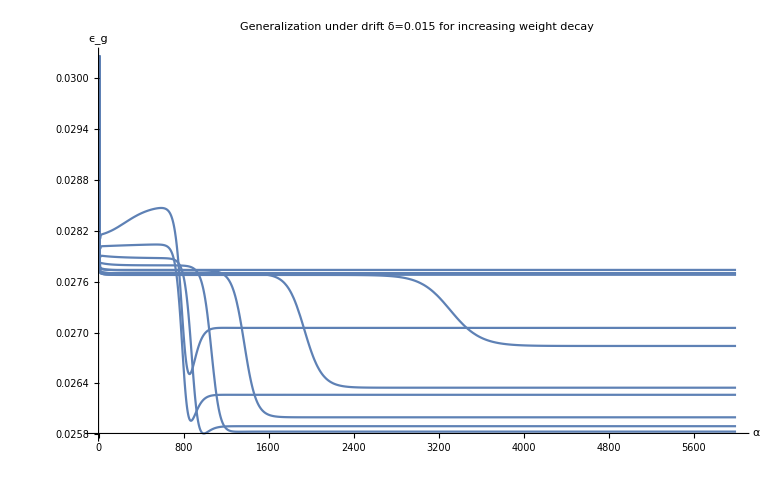

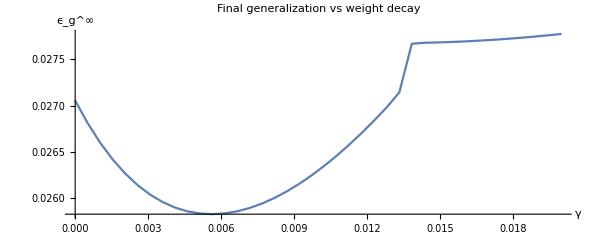

```mathematica
(*Reproducing figure 5b of the Entropy 2018 paper*)
maxAlpha=6000;
getEg[gamma_]:=(ODEsys=FormulateDynamics["Erf","Erf",0.015,gamma];
s=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];
egerr[α_]=ODEsys[generr]/.s;
(*Print[gamma];*)
Return[<|sol->s,egfinal->egerr[6000]|>]
);
(*Slight real target drift*)
δ=0.015;
gammas=Array[#&,40,{0,0.02}];
(*Apply to all values in gammas*)
egs=Map[getEg,gammas];

(*Plot all the generalization errors in one graph*)
Plot[Table[ODEsys[generr]/.egs[[i]][sol],{i,1,40,4}],{α,0,6000},AxesLabel->{"α","ϵ_g"},PlotLabel->"Generalization under drift δ=0.015 for increasing weight decay"]

(*Plot weight decay γ parameter vs Subscript[ϵ, g]^∞*)
egfinals=Map[Function[x,x[egfinal]],egs];
(*ListPlot[Transpose[{gammas,egfinals}],AxesLabel->{"γ","ϵ_g^∞"}]*)
ListCurvePathPlot[Transpose[{gammas,egfinals}],AxesLabel->{"γ","ϵ_g^∞"},AspectRatio->Full,PlotLabel->"Final generalization vs weight decay"]
```

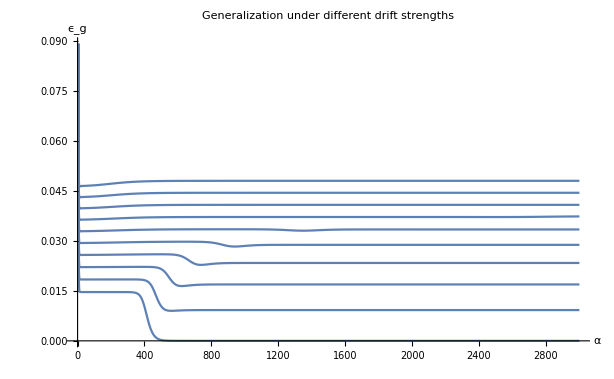

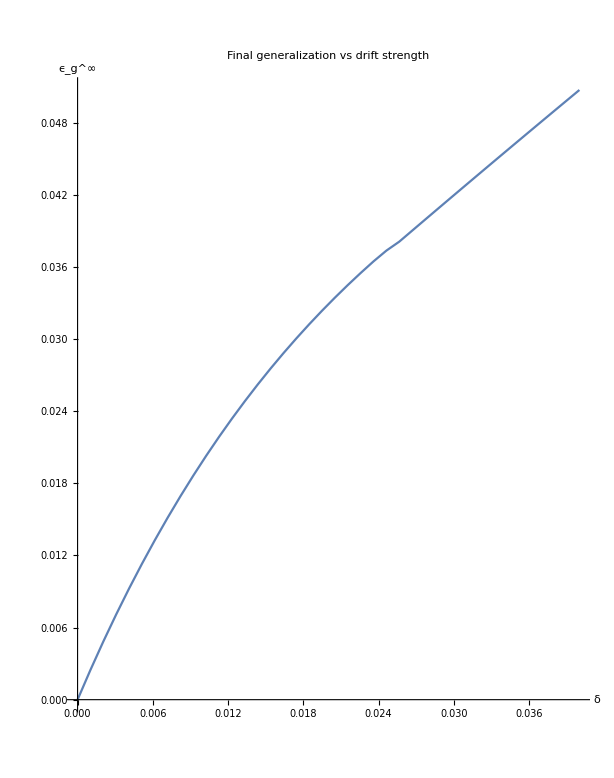

```mathematica
(*Reproducing figure 5a from Entropy 2018 paper*)
maxAlpha=3000;
getEg2[delta_]:=(ODEsys=FormulateDynamics["Erf","Erf",delta,0];
s=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];
egerr[α_]=ODEsys[generr]/.s;
(*Print[gamma];*)
Return[<|sol->s,egfinal->egerr[3000]|>]
);
γ=0;
deltas=Array[#&,40,{0,0.04}];
egs2=Map[getEg2,deltas];

(*Plot all the generalization errors in one graph*)
Plot[Table[ODEsys[generr]/.egs2[[i]][sol],{i,1,40,4}],{α,0,3000},AxesLabel->{"α","ϵ_g"},PlotLabel->"Generalization under different drift strengths"]

(*Plot weight decay γ parameter vs Subscript[ϵ, g]^∞*)
egfinals=Map[Function[x,x[egfinal]],egs2];
ListCurvePathPlot[Transpose[{deltas,egfinals}],AxesLabel->{"δ","ϵ_g^∞"},AspectRatio->Full,PlotLabel->"Final generalization vs drift strength"]
```

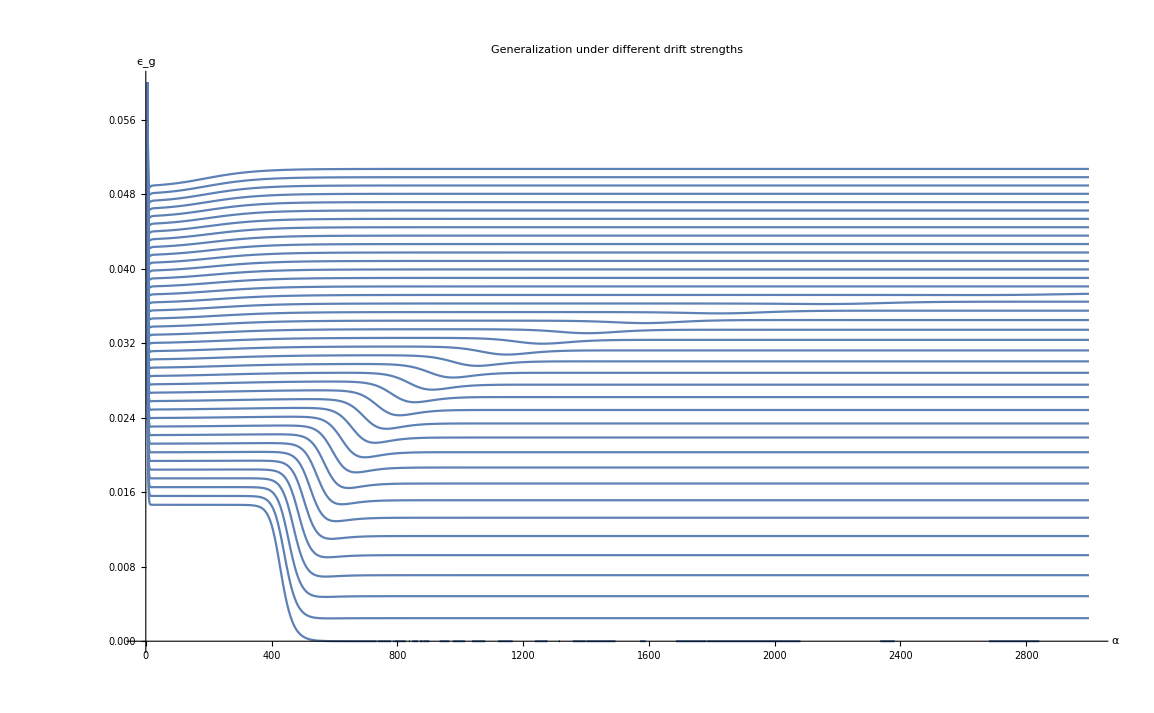

```mathematica
Plot[Table[ODEsys[generr]/.egs2[[i]][sol],{i,1,40,3}],{α,0,3000},AxesLabel->{"α","ϵ_g"},PlotLabel->"Generalization under different drift strengths",PlotRange->{{0,3000},{0,0.06}}]
```